g_n(t)=∑_(n=-N)^N α_n(t)ϕ_n(x)

ψ(x, t) = ∑_(n=-N)^N a_n(t)ϕ_n(x)=(a⃗)^T(t)ϕ⃗

|ψ(x,t)|^2=OverBar[ψ(x, t)]ψ(x,t) 

|ψ(x,t)|^2=∑_(n=-N)^N α(t)ϕ_n(x))

|ψ(x,t)|^2=^?∑_(m=-N)^N OverBar[a_m(t)ϕ_m(x)]∑_(n=-N)^N a_n(t)ϕ_n(x)=∑_(n=-N)^N (∑_(m=-N)^N OverBar[a_m(t)ϕ_m(x)]a_n(t))ϕ_n(x)
α_n=^?∑_(m=-N)^N OverBar[a_m(t)ϕ_m(x)]a_n(t)

```mathematica
b=15.0
```

15.

```mathematica
d=10.0
```

10.

```mathematica
psi[x_]:=Sin[x]
```

```mathematica
prob[x_]:=Conjugate[psi[x]]*psi[x]
```

```mathematica
F=16
```

16

```mathematica
a=N@Table[Integrate[1/(√(2*b))*ⅇ^(-ⅈ*π*m*x/b)*psi[x],{x,-b,b}],{m,-F,F}];
```

```mathematica
recpsi[x_]:=Total[a*Table[1/(√(2*b))*ⅇ^(ⅈ*π*n*x/b),{n,-F,F}]]
```

```mathematica
Norm[Table[(psi[x]-recpsi[x])^2,{x,-d,d,0.001}]]
```

0.0290374

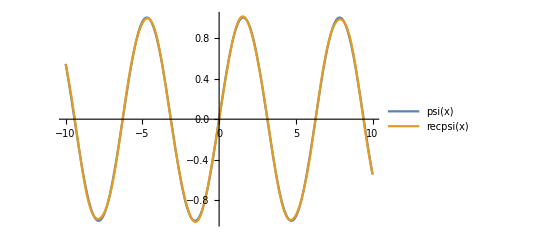

```mathematica
Plot[{psi[x],recpsi[x]},{x,-d,d},PlotLegends->"Expressions"]
```

```mathematica
Total[Table[Conjugate[a]*Conjugate[1/(√(2*b))*ⅇ^(ⅈ*π*m*x/b)],{m, -F, F}]]
```

{(0.+0.0142018 ⅈ)+(0.+0.0142018 ⅈ) ⅇ^((0.-0.20944 ⅈ) Conjugate[x])+30+(0.+0.0142018 ⅈ) ⅇ^((0.+3.35103 ⅈ) Conjugate[x]),1,29,(0.+0.0153554 ⅈ)+31+(0.+0.0153554 ⅈ) ⅇ^1,1}
 |  |  |  |

```mathematica
a=N@Table[Integrate[1/(√(2*b))*ⅇ^(-ⅈ*π*m*x/b)*psi[x],{x,-b,b}],{m,-F,F}];
```

```mathematica
Integrate[1/(√(2*b))*ⅇ^(-ⅈ*π*2*x/b)*1/(√(2*b))*ⅇ^(ⅈ*π*7*x/b),{x,-b,b}]
```

-7.41047×10^-17+0. ⅈ